```mathematica
Quit[]
```

```mathematica
$Assumptions=α∈Reals&&α>0&&m∈Reals&&m>0&&λ∈Reals;
```

```mathematica
ω[p_]:=(*√(m^2+p^2)*)p^2/(2m);Nx=25;max=100;
```

```mathematica
m =5/2;λ=π/2;
```

```mathematica
Clear@α
```

```mathematica
α=(*0.33375*)0.474;
```

```mathematica
ϕ[n_][p_]:=√(α/(√π 2^n n!)) HermiteH[n,α p] E^(1/2 (-α^2) p^2)
```

```mathematica
H[n_][p_?NumberQ]:=ω[p]ϕ[n][p]-λ/π NIntegrate[(ϕ[n][k]-ϕ[n][p]-(k-p)ϕ[n]'[p])/(p-k)^2,{k,-max,0,max}]
```

```mathematica
Table[2NIntegrate[ϕ[2i][p]H[2n][p],{p,0,max},MaxRecursion->10],{i,0,Nx},{n,0,Nx}]//AbsoluteTiming
Sort@Eigenvalues[Last[%]]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 10 recursive bisections in p near {p} = {7.32344}. NIntegrate obtained -0.00346955 and 4.55597×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 10 recursive bisections in p near {p} = {7.32344}. NIntegrate obtained -0.00415321 and 5.26574×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 10 recursive bisections in p near {p} = {7.71407}. NIntegrate obtained -0.00355559 and 5.51893×10^-9 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{6324.8,{{0.838112,0.245283,-0.0904518,-0.0495416,-0.0331014,-0.0244243,-0.0191328,-0.0156004,-0.013091,-0.0112254,-0.0097895,-0.00865353,-0.0077347,-0.00697773,-0.00634444,-0.00580761},{0.259428,3.10278,0.920603,-0.1051,-0.0514936,-0.032074,-0.0225482,-0.0170481,-0.0135291,-0.0111126,-0.00936536,-0.00805128,-0.0070319,-0.00622113,-0.00556288,-0.00501918},{-0.0904485,0.95526,5.0905,1.60728,-0.122987,-0.0576905,-0.0347772,-0.0238349,-0.0176589,-0.0137836,-0.0111668,-0.00930228,-0.00791793,-0.00685621,-0.00602031,-0.0053478},{-0.0495416,-0.105087,1.6621,6.99514,2.30822,-0.139291,-0.0638678,-0.0377905,-0.0255025,-0.0186501,-0.0143969,-0.011553,-0.00954454,-0.00806529,-0.00693909,-0.00605835},{-0.0331014,-0.0514936,-0.12296,2.38312,8.85477,3.01924,-0.15411,-0.0696896,-0.0407467,-0.0272151,-0.0197245,-0.0151067,-0.0120385,-0.00988436,-0.00830643,-0.00711118},{-0.0244243,-0.032074,-0.0576905,-0.139243,3.11423,10.685,3.73767,-0.167731,-0.0751469,-0.0435773,-0.0288929,-0.0208037,-0.01584,-0.0125564,-0.0102605,-0.00858532},{-0.0191328,-0.0225482,-0.0347772,-0.0638677,-0.154037,3.85273,12.494,4.46179,-0.180383,-0.0802792,-0.0462747,-0.0305142,-0.0218621,-0.0165707,-0.0130815,-0.0106492},{-0.0156004,-0.0170481,-0.0238349,-0.0377905,-0.0696895,-0.167627,4.59694,14.2868,5.19045,-0.19224,-0.0851293,-0.0488469,-0.0320748,-0.022891,-0.0172884,-0.0136029},{-0.013091,-0.0135291,-0.0176589,-0.0255025,-0.0407467,-0.0751467,-0.180243,5.34569,16.0666,5.92284,-0.203432,-0.0897346,-0.0513054,-0.0335766,-0.0238882,-0.017989},{-0.0112254,-0.0111126,-0.0137836,-0.0186501,-0.0272151,-0.0435773,-0.0802789,-0.192058,6.09818,17.8358,6.65835,-0.214057,-0.0941262,-0.0536616,-0.0350233,-0.0248538},{-0.0097895,-0.00936536,-0.0111668,-0.0143969,-0.0197245,-0.0288929,-0.0462747,-0.0851289,-0.203203,6.85379,19.596,7.39652,-0.224193,-0.0983299,-0.0559258,-0.0364191},{-0.00865353,-0.00805128,-0.00930228,-0.011553,-0.0151067,-0.0208037,-0.0305142,-0.0488469,-0.089734,-0.213775,7.61208,21.3486,8.13701,-0.233901,-0.102367,-0.058107},{-0.00773469,-0.0070319,-0.00791793,-0.00954454,-0.0120385,-0.01584,-0.0218621,-0.0320748,-0.0513054,-0.0941254,-0.223852,8.3727,23.0946,8.87952,-0.243232,-0.106255},{-0.00697773,-0.00622113,-0.00685621,-0.0080653,-0.00988436,-0.0125564,-0.0165707,-0.022891,-0.0335766,-0.0536616,-0.0983289,-0.233497,9.13534,24.8347,9.62383,-0.252227},{-0.00634444,-0.00556288,-0.00602031,-0.0069391,-0.00830644,-0.0102605,-0.0130815,-0.0172884,-0.0238882,-0.0350233,-0.0559258,-0.102366,-0.242759,9.8998,26.5696,10.3697},{-0.00580761,-0.00501918,-0.0053478,-0.00605835,-0.00711118,-0.00858532,-0.0106492,-0.0136029,-0.017989,-0.0248538,-0.0364191,-0.058107,-0.106253,-0.251678,10.6659,28.2998}}}

{0.800113,2.56202,3.80448,4.87068,5.89085,7.05524,8.49553,10.2443,12.3222,14.7529,17.5835,20.8666,24.7107,29.2447,34.8133,41.9756}

```mathematica
2NIntegrate[ϕ[30][p]H[30][p],{p,0,200},MaxRecursion->10]//Timing
```

{47.3281,28.2998}

```mathematica
NIntegrate[ϕ[30][p]H[30][p],{p,-max,max},MaxRecursion->10]//Timing
```

{71.3281,28.2943}

```mathematica
NIntegrate[ϕ[30][p]H[30][p],{p,-max,max},MaxRecursion->50]//Timing
```

{77.3281,28.2998}

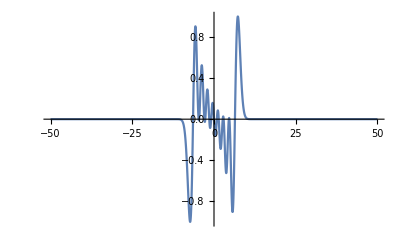

```mathematica
Plot[ϕ[6][p]H[9][p],{p,-50,50},PlotRange->All]
```

```mathematica
Last@%19//MatrixForm
```

(6.72374 | 0 | 3.4277 | 0 | -0.975301 | 0 | 0.41917 | 0 | -0.293982 | 0 | 0.169398 | 0 | -0.145569 | 0 | 0.0912165 | 0 | -0.0872037 | 0 | 0.0562689 | 0 | -0.0579406 | 0 | 0.03761 | 0 | -0.0411226 | 0
0 | 12.1597 | 0 | 4.21381 | 0 | -1.00159 | 0 | 0.395163 | 0 | -0.249204 | 0 | 0.140854 | 0 | -0.110203 | 0 | 0.0702679 | 0 | -0.0609734 | 0 | 0.0411676 | 0 | -0.0381055 | 0 | 0.026529 | 0 | -0.0257252
3.47236 | 0 | 15.2069 | 0 | 5.14578 | 0 | -1.24789 | 0 | 0.498974 | 0 | -0.324987 | 0 | 0.18399 | 0 | -0.14977 | 0 | 0.0942759 | 0 | -0.0858464 | 0 | 0.0563766 | 0 | -0.0553223 | 0 | 0.0368978 | 0
0 | 4.29142 | 0 | 18.0185 | 0 | 5.80019 | 0 | -1.34677 | 0 | 0.525327 | 0 | -0.32777 | 0 | 0.184837 | 0 | -0.143551 | 0 | 0.0916168 | 0 | -0.0789891 | 0 | 0.0534725 | 0 | -0.0491879 | 0 | 0.0343748
-0.975036 | 0 | 5.25591 | 0 | 20.2878 | 0 | 6.4667 | 0 | -1.51308 | 0 | 0.592683 | 0 | -0.375839 | 0 | 0.211705 | 0 | -0.168252 | 0 | 0.106331 | 0 | -0.094508 | 0 | 0.0627265 | 0 | -0.0599836 | 0
0 | -1.00099 | 0 | 5.94287 | 0 | 22.4249 | 0 | 7.01772 | 0 | -1.61385 | 0 | 0.625853 | 0 | -0.388079 | 0 | 0.218676 | 0 | -0.169003 | 0 | 0.107996 | 0 | -0.0926799 | 0 | 0.0628965 | 0 | -0.0575825
0.419174 | 0 | -1.24684 | 0 | 6.64207 | 0 | 24.3081 | 0 | 7.56276 | 0 | -1.7462 | 0 | 0.678066 | 0 | -0.424473 | 0 | 0.238754 | 0 | -0.187297 | 0 | 0.118768 | 0 | -0.104076 | 0 | 0.0695879 | 0
0 | 0.395176 | 0 | -1.34514 | 0 | 7.22597 | 0 | 26.1025 | 0 | 8.04441 | 0 | -1.84188 | 0 | 0.711828 | 0 | -0.439685 | 0 | 0.247738 | 0 | -0.190813 | 0 | 0.122098 | 0 | -0.104421 | 0 | 0.0710274
-0.293982 | 0 | 0.499 | 0 | -1.51076 | 0 | 7.8041 | 0 | 27.7456 | 0 | 8.51628 | 0 | -1.95502 | 0 | 0.755694 | 0 | -0.469668 | 0 | 0.264144 | 0 | -0.205576 | 0 | 0.130738 | 0 | -0.11352 | 0
0 | -0.249204 | 0 | 0.525372 | 0 | -1.61068 | 0 | 8.31907 | 0 | 29.3235 | 0 | 8.94806 | 0 | -2.04497 | 0 | 0.788491 | 0 | -0.485807 | 0 | 0.273801 | 0 | -0.210372 | 0 | 0.134797 | 0 | -0.114977
0.169398 | 0 | -0.324986 | 0 | 0.592755 | 0 | -1.74206 | 0 | 8.82451 | 0 | 30.7992 | 0 | 9.36963 | 0 | -2.14554 | 0 | 0.827013 | 0 | -0.511739 | 0 | 0.287924 | 0 | -0.222916 | 0 | 0.142121 | 0
0 | 0.140854 | 0 | -0.327768 | 0 | 0.625963 | 0 | -1.83662 | 0 | 9.29011 | 0 | 32.2242 | 0 | 9.76351 | 0 | -2.23026 | 0 | 0.858434 | 0 | -0.528008 | 0 | 0.297719 | 0 | -0.228333 | 0 | 0.146499
-0.145569 | 0 | 0.183991 | 0 | -0.375835 | 0 | 0.678226 | 0 | -1.94848 | 0 | 9.74577 | 0 | 33.5749 | 0 | 10.1477 | 0 | -2.32186 | 0 | 0.893195 | 0 | -0.551141 | 0 | 0.310286 | 0 | -0.239361 | 0
0 | -0.110203 | 0 | 0.184837 | 0 | -0.388074 | 0 | 0.712051 | 0 | -2.037 | 0 | 10.174 | 0 | 34.8845 | 0 | 10.5116 | 0 | -2.40203 | 0 | 0.923183 | 0 | -0.567201 | 0 | 0.319983 | 0 | -0.245072
0.0912165 | 0 | -0.14977 | 0 | 0.211705 | 0 | -0.424464 | 0 | 0.755997 | 0 | -2.13597 | 0 | 10.5929 | 0 | 36.1371 | 0 | 10.8665 | 0 | -2.48685 | 0 | 0.955118 | 0 | -0.588275 | 0 | 0.331421 | 0
0 | 0.0702679 | 0 | -0.143551 | 0 | 0.218677 | 0 | -0.439671 | 0 | 0.788891 | 0 | -2.21893 | 0 | 10.9917 | 0 | 37.3557 | 0 | 11.2059 | 0 | -2.56308 | 0 | 0.983733 | 0 | -0.603983 | 0 | 0.340912
-0.0872037 | 0 | 0.0942759 | 0 | -0.168252 | 0 | 0.238755 | 0 | -0.469649 | 0 | 0.827533 | 0 | -2.30858 | 0 | 11.3819 | 0 | 38.5288 | 0 | 11.5371 | 0 | -2.64258 | 0 | 1.01344 | 0 | -0.623473 | 0
0 | -0.0609734 | 0 | 0.0916168 | 0 | -0.169003 | 0 | 0.247739 | 0 | -0.485779 | 0 | 0.859098 | 0 | -2.38661 | 0 | 11.7568 | 0 | 39.6731 | 0 | 11.856 | 0 | -2.71542 | 0 | 1.04077 | 0 | -0.638772
0.0562689 | 0 | -0.0858464 | 0 | 0.106331 | 0 | -0.187297 | 0 | 0.264145 | 0 | -0.5117 | 0 | 0.89403 | 0 | -2.4691 | 0 | 12.1239 | 0 | 40.7801 | 0 | 12.1674 | 0 | -2.79063 | 0 | 1.06865 | 0
0 | 0.0411676 | 0 | -0.0789891 | 0 | 0.107996 | 0 | -0.190813 | 0 | 0.273804 | 0 | -0.527954 | 0 | 0.924222 | 0 | -2.54279 | 0 | 12.479 | 0 | 41.8623 | 0 | 12.4687 | 0 | -2.86053 | 0 | 1.0948
-0.0579406 | 0 | 0.0563766 | 0 | -0.094508 | 0 | 0.118768 | 0 | -0.205576 | 0 | 0.287927 | 0 | -0.551069 | 0 | 0.956396 | 0 | -2.61953 | 0 | 12.827 | 0 | 42.9131 | 0 | 12.7633 | 0 | -2.9322 | 0
0 | -0.0381055 | 0 | 0.0534725 | 0 | -0.0926799 | 0 | 0.122098 | 0 | -0.210371 | 0 | 0.297724 | 0 | -0.567106 | 0 | 0.985288 | 0 | -2.68938 | 0 | 13.1652 | 0 | 43.9423 | 0 | 13.0494 | 0 | -2.99956
0.03761 | 0 | -0.0553223 | 0 | 0.0627265 | 0 | -0.104076 | 0 | 0.130738 | 0 | -0.222915 | 0 | 0.310294 | 0 | -0.588151 | 0 | 1.01532 | 0 | -2.76136 | 0 | 13.4971 | 0 | 44.9448 | 0 | 13.3293 | 0
0 | 0.026529 | 0 | -0.0491879 | 0 | 0.0628965 | 0 | -0.104421 | 0 | 0.134797 | 0 | -0.228333 | 0 | 0.319994 | 0 | -0.603822 | 0 | 1.04302 | 0 | -2.82778 | 0 | 13.8208 | 0 | 45.9281 | 0 | 13.6021
-0.0411226 | 0 | 0.0368978 | 0 | -0.0599836 | 0 | 0.0695879 | 0 | -0.11352 | 0 | 0.142121 | 0 | -0.23936 | 0 | 0.331436 | 0 | -0.623267 | 0 | 1.07134 | 0 | -2.8957 | 0 | 14.1389 | 0 | 46.8882 | 0
0 | -0.0257252 | 0 | 0.0343748 | 0 | -0.0575825 | 0 | 0.0710274 | 0 | -0.114977 | 0 | 0.146499 | 0 | -0.24507 | 0 | 0.340933 | 0 | -0.63851 | 0 | 1.09797 | 0 | -2.95904 | 0 | 14.4501 | 0 | 47.8313)

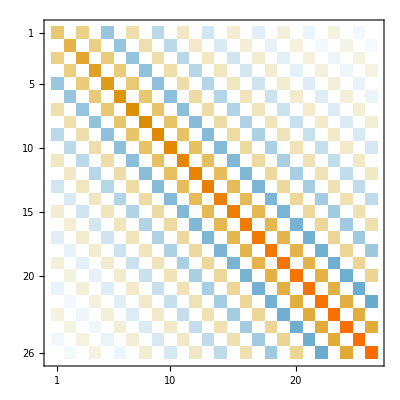

```mathematica
MatrixPlot[%21]
```